```mathematica
slope[pointpair_]:=Module[{x1,x2,y1,y2,answer},
x1=pointpair[[1,1]];
y1=pointpair[[1,2]];
x2=pointpair[[2,1]];
y2=pointpair[[2,2]];
If[x1==x2,Print["vertical"];Break[]];
answer=(y1-y2)/(x1-x2);
Return[answer]]
```

```mathematica
yintercept[pointpair_]:=Module[{x1,x2,y1,y2,answer},
x1=pointpair[[1,1]];
y1=pointpair[[1,2]];
x2=pointpair[[2,1]];
y2=pointpair[[2,2]];
If[x1==x2,Print["vertical"];Break[]];
answer=(-x2 y1+x1 y2)/(x1-x2);
Return[answer]]
```

```mathematica
stream=OpenRead["realfxptsprecision1000no1"];
ls=ReadList[stream];
Close[stream]
```

realfxptsprecision1000no1

```mathematica
Length[ls]
```

200

```mathematica
Clear[list];
stream1=OpenRead["realfxNrhoNrun1jun16no11"];
list=ReadList[stream1];
Close[stream1]
```

realfxNrhoNrun1jun16no11

```mathematica
Length[list]
```

1000

means slopes

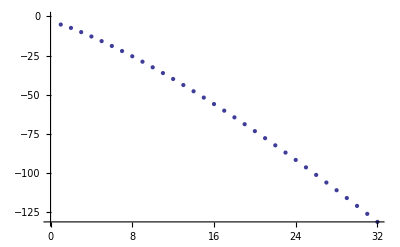

```mathematica
precision=1000;
meansslopes={};
meansintercepts={};
For[n=0,n<50,n++;
slopes={};
intercepts={};

backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]
] (* append *)
](* if loop *)

];(* For loop *)

logdistances={};
For[k=1,k<Length[backorbit],k++;
zr=backorbit[[k]];
logdistance=Re[Log[Abs[(zr-fx)]]];
logdistances=Append[logdistances,{k,logdistance}];
el=Length[logdistances];
If[el>1,
point1=logdistances[[el]];
point2=logdistances[[el-1]];
pointpair={point1,point2};
m=slope[pointpair];
b=yintercept[pointpair];
slopes=Append[slopes,m];
intercepts=Append[intercepts,b]
] (* If loop *)
]; (* k loop *)


meansslopes=Append[meansslopes,{n,Mean[slopes]}];
meansintercepts=Append[meansintercepts,{n,Mean[intercepts]}];

]; (* n loop *)
Print["means slopes"];
Print[ListPlot[meansslopes]];
Print["means intercepts"];
Print[ListPlot[meansintercepts]]


 leaf5point12left
```

## leaf5point12right

means intercepts